## Position from Velocity - Using Lists

## January 16, 2025

My notebook PositionFromVelocity.nb used associations. Perhaps that was unnecessarily fancy, especially at this point in our course when the only two variable we are trying to keep track of are the time and the position.

A list, where the first element is time and the second element is the position will do.

### State As a List

The core limitation of List and NestList are that the function being nested can only take and return one argument. So here are trick is to to put the state (the time and the position) into a list, and make that our argument.

Here is a list that holds the current time and the current position of a particle moving in one dimension:

```mathematica
stateAsAList ={3600,10000}
```

{3600,10000}

Here is a function that adds 1 to the time and 1 to the position:

```mathematica
addOne[l_]:=(
newTime = l[[1]]+1;
newPosition = l[[2]]+1;
{newTime, newPosition}
)
```

Let’s see if it works:

```mathematica
addOne[{3600,10000}]
```

{3601,10001}

So we are now able to use Nest and NestList with functions that have the time and the position in a list:

```mathematica
NestList[addOne, {3600,10000}, 5]
```

{{3600,10000},{3601,10001},{3602,10002},{3603,10003},{3604,10004},{3605,10005}}

### Numerical Integration

We still have our core formulas for moving ahead in time by Δt:

t_2=t_1+Δt

x(t_2)=x(t_1)+v(t_1+Δt/2)*Δt

### Constant Velocity

By far the simplest example is constant velocity. Let’s just have a constant velocity of 3 and a time step of 0.01.

```mathematica
move[l_]:=(
newTime = l[[1]]+0.1;
newPosition = l[[2]]+ 3 * 0.1;
(newTime, newPosition}
)
```

By far the simplest example is constant velocity. Let’s just have a constant velocity of 3 and a time step of 0.1. Then we need to do 15 steps to get from 2.0 to 3.5. Where should we start the particle? How about at time 2.0 we say it was at position -2.0?

```mathematica
NestList[move,<|"time"->2.0, "position"->-2.0|>,15]
```

{<|time→2.,position→-2.|>,<|time→2.1,position→-1.7|>,<|time→2.2,position→-1.4|>,<|time→2.3,position→-1.1|>,<|time→2.4,position→-0.8|>,<|time→2.5,position→-0.5|>,<|time→2.6,position→-0.2|>,<|time→2.7,position→0.1|>,<|time→2.8,position→0.4|>,<|time→2.9,position→0.7|>,<|time→3.,position→1.|>,<|time→3.1,position→1.3|>,<|time→3.2,position→1.6|>,<|time→3.3,position→1.9|>,<|time→3.4,position→2.2|>,<|time→3.5,position→2.5|>}

By far the simplest example is constant velocity. Let’s just have a constant velocity of 3 and a time step of 0.1. Then we need to do 15 steps to get from 2.0 to 3.5. Where should we start the particle? How about at time 2.0 we say it was at position -2.0?

### A Bounce

Let’s have the particle go at constant velocity of 6 until the time is 3.0, and then bounce and go -6 after that:

```mathematica
bounce[a_]:=(
deltaT=0.01;
time = a[["time"]];
position = a[["position"]];
newTime = time+deltaT;
midpointTime =time +deltaT/2;
midpointVelocity = If[midpointTime<3.0,6, -6];
newPosition = position+ midpointVelocity * deltaT;
<|"time"->newTime, "position"->newPosition|>
)
```

I cranked down the Δt to 0.1, and so I am going to have to crank up the number of steps to 150, and I am going to suppress the output:

```mathematica
lotsaPositions = NestList[bounce,<|"time"->2.0, "position"->-2.0|>,150];
```

### Displaying the Bounce

```mathematica
allThePositions = lotsaPositions[[All,"position"]];
```

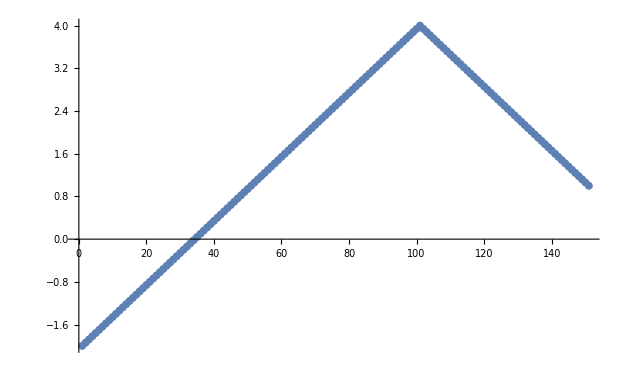

```mathematica
ListPlot[allThePositions]
```

The bounce at t=3.0 occurs at the 100th time step. The plot might look a little jaggy if viewed at low resolution, but it is entirely smooth when enlarged.